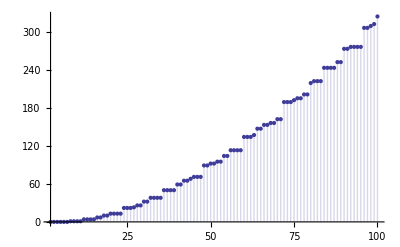

```mathematica
D3[n_] := -1+Floor[n^(1/3)]^3-3∑_(k=2)^Floor[n^(1/3)] (Floor[n/k^2]+ Floor[√(n/k)]^2-2Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}])
DiscretePlot[D3[n],{n,2,100}]
```

```mathematica
DD[ k_, a_, n_ ] := Sum[(-1)^(j+1) Binomial[k,j] DD[ k-j, m, Floor[n/(m^j)]], {m,a, n^(1/k)},{j,1,k}]
DD[ 1,a_, n_ ]:= Floor[n]-a+1
DD[0,a_,n_] := 1
DS[ n_, k_ ] := DD[k,2,n]
DDD[n_, k_ ] := Sum[ DDD[n/j, k-1],{j,2,n}]
DDD[n_,0] := 1
```

```mathematica
D2a[n_] := Sum[ Binomial[3,2](Sum[Binomial[2,1]Binomial[1,0]Sum[1,{m,j,Floor[(n/(j k))]}]-Binomial[2,0],{j,k,Floor[(n/k)^(1/2)]}]) - Binomial[3,1](Sum[1,{m,k,Floor[n/(k^2)]}]) + Binomial[3,0], {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2a[1000]
```

11217

```mathematica
DDD[1000,3]
```

11217

```mathematica
D2b[n_] := Sum[ 3(Sum[2Sum[1,{m,j,Floor[(n/(j k))]}]-1,{j,k,Floor[(n/k)^(1/2)]}]) - 3(Sum[1,{m,k,Floor[n/(k^2)]}]) + 1, {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b[1000]
```

11217

```mathematica
D2b1[n_] := Sum[ 3(Sum[2Sum[1,{m,j,Floor[(n/(j k))]}],{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b2[n_] := Sum[ 3(Sum[-1,{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b3[n_] := Sum[ -3(Sum[1,{m,k,Floor[n/(k^2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b4[n_] := Sum[ 1, {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2Ba[n_] := D2b1[n] + D2b2[n] + D2b3[n] + D2b4[n]
```

```mathematica
D2Ba[1000]
```

11217

```mathematica
D2b1[100]
```

462

```mathematica
D2b1a[100]
```

462

```mathematica
D2b1a[n_] := Sum[ 3(Sum[2(Floor[(n/(j k))]-j+1),{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b1a1[n_] := Sum[ 3(Sum[2(Floor[(n/(j k))]),{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b1a2[n_] := Sum[ 3(Sum[2(-j+1),{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2Bb[n_] := D2b1a1[n] + D2b1a2[n] + D2b2[n] + D2b3[n] + D2b4[n]
```

```mathematica
D2Bb[1000]
```

11217

```mathematica
D2b1a2[n]
```

∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])

```mathematica
D2b1a2[n] + D2b2[n] + D2b3[n] + D2b4[n]
```

-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])

```mathematica
FFF[n_] :=-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])
```

```mathematica
GGG[n_] := D2b1a1[n]+FFF[n]
```

```mathematica
GGG[1000]
```

11217

```mathematica
Expand[-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])]
```

```mathematica
FullSimplify[-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])]
```

-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])

```mathematica
D2b1a1[n_] := Sum[ 3(Sum[2(Floor[(n/(j k))]),{j,k,Floor[(n/k)^(1/2)]}]), {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2b1a1[n_] := 6Sum[ Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}], {k,2,Floor[n^(1/3)]}]
```

```mathematica
FFF[n_] :=-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 (1-k+Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] 3 (-1+k-Floor[√(n/k)]) (-2+k+Floor[√(n/k)])
FFF[n_] :=-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] (-3+3 k-3 Floor[n/k^2])+∑_(k=2)^Floor[n^(1/3)] (-3+3 k-3 Floor[√(n/k)])+∑_(k=2)^Floor[n^(1/3)] (6-9 k+3 k^2+3 Floor[√(n/k)]-3 Floor[√(n/k)]^2)
FFF[n_] :=-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] (-3 k+3 k^2-3 Floor[n/k^2]-3 Floor[√(n/k)]^2)
```

```mathematica
FFF[n_] :=-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 k+∑_(k=2)^Floor[n^(1/3)] 3 k^2+∑_(k=2)^Floor[n^(1/3)] -3 Floor[n/k^2]+∑_(k=2)^Floor[n^(1/3)] -3 Floor[√(n/k)]^2
FFF[n_] :=-1+Floor[n^(1/3)]^3+∑_(k=2)^Floor[n^(1/3)] -3 Floor[n/k^2]+∑_(k=2)^Floor[n^(1/3)] -3 Floor[√(n/k)]^2
```

```mathematica
AAA[n_] := 6Sum[ Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}], {k,2,Floor[n^(1/3)]}]
FFF[n_] :=-1+Floor[n^(1/3)]^3-3∑_(k=2)^Floor[n^(1/3)] (Floor[n/k^2]+ Floor[√(n/k)]^2)
GGG[n_] := AAA[n]+FFF[n]
```

```mathematica
GGG[1000]
```

11217

```mathematica
FullSimplify[-3+3 k-3 Floor[n/k^2]-3+3 k-3 Floor[√(n/k)]+6-9 k+3 k^2+3 Floor[√(n/k)]-3 Floor[√(n/k)]^2]
```

```mathematica
Expand[3 ((-1+k) k-Floor[n/k^2]-Floor[√(n/k)]^2)]
```

-3 k+3 k^2-3 Floor[n/k^2]-3 Floor[√(n/k)]^2

```mathematica
-1+Floor[n^(1/3)]+∑_(k=2)^Floor[n^(1/3)] -3 k+∑_(k=2)^Floor[n^(1/3)] 3 k^2+∑_(k=2)^Floor[n^(1/3)] -3 Floor[n/k^2]+∑_(k=2)^Floor[n^(1/3)] -3 Floor[√(n/k)]^2
```

```mathematica
FullSimplify[-1+Floor[n^(1/3)]-3/2 (-2+Floor[n^(1/3)]+Floor[n^(1/3)]^2)+1/2 (-6+Floor[n^(1/3)]+3 Floor[n^(1/3)]^2+2 Floor[n^(1/3)]^3)+∑_(k=2)^Floor[n^(1/3)] -3 Floor[n/k^2]+∑_(k=2)^Floor[n^(1/3)] -3 Floor[√(n/k)]^2]
```

-1+Floor[n^(1/3)]^3+∑_(k=2)^Floor[n^(1/3)] -3 Floor[n/k^2]+∑_(k=2)^Floor[n^(1/3)] -3 Floor[√(n/k)]^2

```mathematica
AAA[n_] := 6Sum[ Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}], {k,2,Floor[n^(1/3)]}]
FFF[n_] :=-1+Floor[n^(1/3)]^3-3∑_(k=2)^Floor[n^(1/3)] (Floor[n/k^2]+ Floor[√(n/k)]^2-2Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}])
GGG[n_] := AAA[n]+FFF[n]
```

```mathematica
D3[n_] := -1+Floor[n^(1/3)]^3-3∑_(k=2)^Floor[n^(1/3)] (Floor[n/k^2]+ Floor[√(n/k)]^2-2Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}])
```

```mathematica
D3[1000]
```

11217

```mathematica
II[n_] := -1+Floor[n^(1/3)]^3-3∑_(k=2)^Floor[n^(1/3)] (Floor[n/k^2]+ Floor[√(n/k)]^2)
```

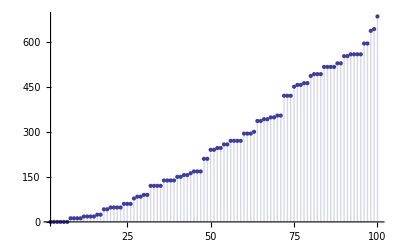

```mathematica
DiscretePlot[AAA[n],{n,2,100}]
```

```mathematica
DiscretePlot[DDD[n,3],{n,2,100}]
```

-Graphics-

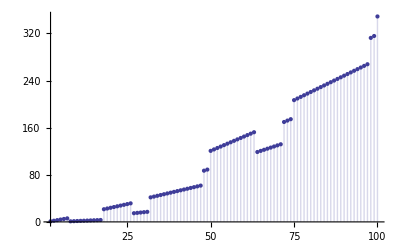

```mathematica
D3a[n_] := -1+(n^(1/3))^3-3∑_(k=2)^(n^(1/3)) ((n/k^2)+ (√(n/k))^2-2Sum[n/j/k,{j,k,(n/k)^.5}])
DiscretePlot[D3a[n],{n,2,100}]
```

```mathematica
D3a[n_] := -1+(n^(1/3))^3-3∑_(k=2)^(n^(1/3)) ((n/k^2)+ (√(n/k))^2-2Sum[n/j/k,{j,k,(n/k)^.5}])
```

```mathematica
Plot[Floor[ n^(1/3)] Floor[(n/Floor[ n^(1/3)])^(1/2)],{n,1,1000}]
```

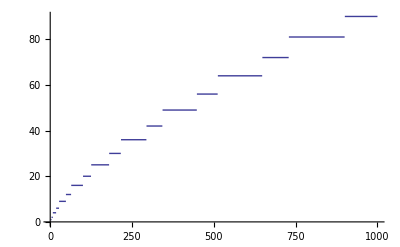

```mathematica
AAB[n_] := Sum[ Sum[Floor[n/j/k],{j,k,Floor[(n/k)^.5]}], {k,2,Floor[n^(1/3)]}]
```

```mathematica
AA[n_, a_,k_ ] := Sum[ AA[n/j,j,k-1],{j,a, Floor[n^(1/k)]}]
```

```mathematica
AA[n_, a_, 1 ] := Floor[n]
```

```mathematica
AA[64,2,3]
```

56

```mathematica
AAB[100]
```

114

```mathematica
BB[ n_ ] := Sum[ AA[n,2,k](k-1)! (-1)^k, {k,2,20}]
```

```mathematica
BB[64]
```

260

```mathematica
Table[ AA[63,2,k],{k,1,8}]
```

{63,98,50,15,3,0,0,0}

```mathematica
Table[AA[64,2,k],{k,1,8}]
```

{64,108,56,20,4,2,0,0}

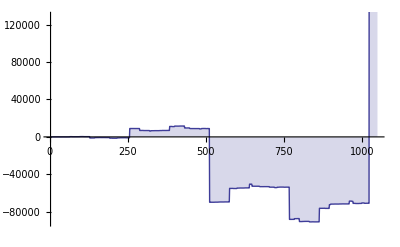

```mathematica
DiscretePlot[ BB[n],{n,2,1050}]
```